```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataa=Import["fans-20180901-06-10w+.csv"];
Dimensions@dataa
```

{1514,7}

```mathematica
datab=Import["fans-20180906-16-5k+.csv"];
Dimensions@datab
```

{29427,39}

## 筛选50w+

```mathematica
upa=Pick[dataa⟦2;;-1,1⟧,Table[Max[dataa⟦i,2;;-1⟧]>500000,{i,2,1514}],True];
Dimensions@upa
```

{222}

```mathematica
upb=Pick[datab⟦2;;-1,1⟧,Table[Max[DeleteCases[datab⟦i,2;;-1⟧,""]]>500000,{i,2,29427}],True];
Dimensions@upb
```

{229}

```mathematica
upA=upa∪upb;
```

```mathematica
Dimensions@upA
```

{229}

```mathematica
temp=Complement[upb,upa]
```

{2929048,7005369,8366990,16539048,99157282,175861153,250858633}

```mathematica
temp2=temp;
Do[temp2⟦i⟧=("fans"/.("card"/.("data"/.Import["http"<>If[OddQ@i,"s",""]<>"://api.bilibili.com/x/web-interface/card?mid="<>ToString[temp⟦i⟧],"JSON"]))),
{i,Length@temp}];
temp2
```

{503234,506887,524409,533909,575668,512867,1225109}

```mathematica
temp3=temp;
Do[temp3⟦i⟧=("name"/.("card"/.("data"/.Import["http"<>If[OddQ@i,"s",""]<>"://api.bilibili.com/x/web-interface/card?mid="<>ToString[temp⟦i⟧],"JSON"]))),
{i,Length@temp}];
temp3
```

{网易暴雪游戏视频,剑网3官方视频,欣小萌有点污,一只小仙若,盗月社食遇记,大胃mini,华农兄弟}

```mathematica
Joini[i_]:=Join[Select[dataa⟦2;;-1,All⟧,#⟦1⟧==upa⟦i⟧&]⟦1⟧,Drop[Select[datab⟦2;;-1,All⟧,#⟦1⟧==upa⟦i⟧&]⟦1⟧,1]]
```

```mathematica
Export["select50w+.csv",Table[Joini@i,{i,1,Length@upa}]];
```

```mathematica
bu[i_]:=Select[datab⟦2;;-1,All⟧,#⟦1⟧==temp⟦i⟧&]⟦1⟧
Export["select50w+bu.csv",Table[bu@i,{i,1,Length@temp}]];
```

## 时间序列重采样

```mathematica
data=Import["select50w+.csv"];
```

```mathematica
Dimensions@data
```

{230,45}

```mathematica
time=data⟦1,2;;-1⟧;
```

```mathematica
todate[i_]:=DateObject@ToExpression@{StringTake[ToString@time⟦i⟧,4],StringTake[ToString@time⟦i⟧,{5,6}],StringTake[ToString@time⟦i⟧,{7,8}],StringTake[ToString@time⟦i⟧,{9,10}]}
```

```mathematica
timeO=Table[todate[i],{i,Length@time}];
```

```mathematica
ts[i_]:=(
p=Pick[Table[{timeO⟦j⟧,data⟦i,j+1⟧},{j,Length@timeO}],
Table[data⟦i,j+1⟧≠"",{j,Length@timeO}]];
TimeSeries[p⟦All,2⟧,{p⟦All,1⟧},ResamplingMethod->{"Interpolation",InterpolationOrder->2}]
)
```

```mathematica
ts[222]
```

TimeSeries[…]

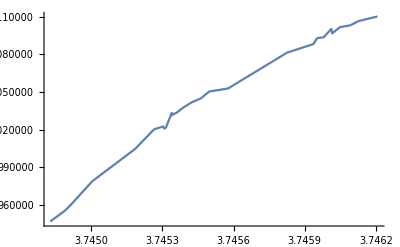

```mathematica
ListLinePlot[ts[222]]
```

```mathematica
rs[i_]:=TimeSeriesResample[ts[i],{DateObject[{2018,9,1,11}],Automatic,0.5},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

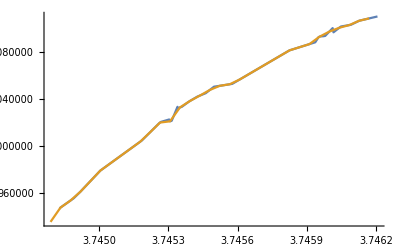

```mathematica
ListLinePlot[{ts[222],rs[222]}]
```

```mathematica
Export["rs.csv",Join[DateString/@DateObject/@rs[2]["Times"],
Table[Prepend[IntegerPart@rs[i]["Values"],data⟦i,1⟧],{i,2,230}]
]]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

rs.csv

## 掠过的话10w+都要

```mathematica
upa=Pick[dataa⟦2;;-1,1⟧,Table[Max[dataa⟦i,2;;-1⟧]>100000,{i,2,1514}],True];
Dimensions@upa
```

{1494}

```mathematica
upb=Pick[datab⟦2;;-1,1⟧,Table[Max[DeleteCases[datab⟦i,2;;-1⟧,""]]>100000,{i,2,29427}],True];
Dimensions@upb
```

{1834}

```mathematica
upA=upa∪upb;
```

```mathematica
Dimensions@upA
```

{1843}

```mathematica
Joini[i_]:=Join[Select[dataa⟦2;;-1,All⟧,#⟦1⟧==upa⟦i⟧&]⟦1⟧,Drop[Select[datab⟦2;;-1,All⟧,#⟦1⟧==upa⟦i⟧&]⟦1⟧,1]]
```

```mathematica
Export["select10w+.csv",Table[Joini@i,{i,1,Length@upa}]];
```

Part::partw: {} 的部分 1 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
bu[i_]:=Select[datab⟦2;;-1,All⟧,#⟦1⟧==temp⟦i⟧&]⟦1⟧
Export["select10w+bu.csv",Table[bu@i,{i,1,Length@temp}]];
```

## 时间序列重采样

```mathematica
data=Import["select10w+.csv"];
```

```mathematica
Dimensions@data
```

{1508,45}

```mathematica
time=data⟦1,2;;-1⟧;
```

```mathematica
todate[i_]:=DateObject@ToExpression@{StringTake[ToString@time⟦i⟧,4],StringTake[ToString@time⟦i⟧,{5,6}],StringTake[ToString@time⟦i⟧,{7,8}],StringTake[ToString@time⟦i⟧,{9,10}]}
```

```mathematica
timeO=Table[todate[i],{i,Length@time}];
```

```mathematica
ts[i_]:=(
p=Pick[Table[{timeO⟦j⟧,data⟦i,j+1⟧},{j,Length@timeO}],
Table[data⟦i,j+1⟧≠"",{j,Length@timeO}]];
TimeSeries[p⟦All,2⟧,{p⟦All,1⟧},ResamplingMethod->{"Interpolation",InterpolationOrder->2}]
)
```

```mathematica
rs[i_]:=TimeSeriesResample[ts[i],{DateObject[{2018,9,1,11}],Automatic,0.5},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

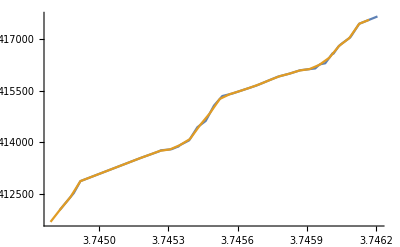

```mathematica
ListLinePlot[{ts[222],rs[222]}]
```

```mathematica
Export["rs10w+.csv",Join[DateString/@DateObject/@rs[2]["Times"],
Table[Prepend[IntegerPart@rs[i]["Values"],data⟦i,1⟧],{i,2,1508}]
]]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

rs10w+.csv

```mathematica
data=Import["rs50w+.csv"];
```

```mathematica
temp=data⟦1,2;;-1⟧;
temp3=temp;
Do[temp3⟦i⟧=("name"/.("card"/.("data"/.Import["http"<>If[OddQ@i,"s",""]<>"://api.bilibili.com/x/web-interface/card?mid="<>ToString[temp⟦i⟧],"JSON"]))),
{i,Length@temp}];
```

```mathematica
Export["cname.csv",temp3,CharacterEncoding->"CP936"]
```

cname.csv